```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

## Ze plot data

```mathematica
pots={344.960,564.480,815.360,1128.960,1790.880,1823.360,2119.040,3153.920,3297.280,3109.120,2903.040,2222.080,1680.000,1868.160,1827.840,2410.240,2607.360,2419.200,3297.280,2903.040,2419.200}; curs={0.072,0.449,1.094,1.482,2.091,1.795,1.710,1.875,1.712,1.613,1.844,1.750,1.773,1.706,1.819,1.694,1.725,1.494,1.985,1.637,1.775}; curErrs={0.013,0.037,0.050,0.056,0.073,0.059,1.701,0.103,0.052,0.057,0.067,0.062,0.068,0.057,0.071,0.066,0.059,0.064,0.078,0.064,0.351};
```

```mathematica
pots={344.960,564.480,815.360,1128.960,1790.880,1823.360,2119.040,3153.920,3297.280,3109.120,2903.040,2222.080,1680.000,1868.160,1827.840,2410.240,2607.360,2419.200,3297.280,2903.040,2419.200,3109.120,3404.800,3360.000,3360.000,3691.520,3153.920,3772.160,3942.400,5967.360,4444.160,4838.400,6594.560,4444.160,4587.520,4193.280,4838.400,5429.760,4838.400,5214.720,4838.400,5214.720,5537.280,5214.720,5214.720,5967.360,7383.041,6809.599,5806.080,6809.599,7598.080,6307.840,6594.560,6594.560,6218.240,7096.320,5797.120,6406.400,5519.360,5402.880,8099.840,7598.080,8099.840,8099.840,7687.680,6720.000,5824.000,4032.000,3360.000,2714.880,2464.000,1769.600,2024.960,1827.840,1827.840,2213.120,2464.000,2213.120,2213.120,2222.080,2419.200,2096.640,2024.960,2024.960,2024.960,1827.840,1899.520,1232.000,1303.680,788.480,1232.000,1146.880,1209.600,616.000,470.400,344.960,344.960,985.600,344.960,344.960,344.960,344.960,344.960}; curs={0.072,0.449,1.094,1.482,2.091,1.795,1.710,1.875,1.712,1.613,1.844,1.750,1.773,1.706,1.819,1.694,1.725,1.494,1.985,1.637,1.775,2.032,2.388,2.322,2.089,1.620,1.707,1.178,1.556,1.875,2.162,2.194,2.392,1.717,1.831,1.890,1.877,1.758,1.799,1.838,2.136,2.521,2.214,1.901,1.968,1.435,1.424,2.087,2.168,1.996,2.001,2.165,1.780,1.883,1.548,2.576,3.412,4.258,5.238,4.815,4.018,2.553,2.447,3.542,3.515,3.820,3.385,2.487,2.367,1.782,1.780,1.628,1.636,1.749,1.708,2.143,2.591,2.683,2.548,2.271,2.462,2.208,2.468,2.240,2.011,2.060,1.718,1.499,1.391,1.463,1.681,0.646,0.592,0.251,0.187,0.240,0.813,0.156,0.165,0.134,0.220,0.217,0.219}; curErrs={0.013,0.037,0.050,0.056,0.073,0.059,1.701,0.103,0.052,0.057,0.067,0.062,0.068,0.057,0.071,0.066,0.059,0.064,0.078,0.064,0.351,0.081,0.092,0.092,0.087,0.073,0.077,0.057,0.097,0.242,0.077,0.111,0.097,0.082,0.089,0.086,0.103,0.093,0.097,0.083,0.104,0.136,0.131,0.104,0.124,0.074,0.387,0.108,0.096,0.146,0.093,0.221,0.142,0.135,0.113,0.153,0.165,0.270,0.225,0.301,0.305,0.182,0.152,0.191,0.248,0.274,0.218,0.199,0.156,0.153,0.209,0.146,0.123,0.281,0.206,0.195,0.086,0.073,0.078,0.082,0.068,0.069,0.071,0.065,0.197,0.130,0.143,0.111,0.103,0.225,0.061,0.095,0.044,0.035,0.024,0.023,0.052,0.021,0.026,0.023,0.026,0.022,0.024};
```

### Data for first and second portions of arc in which we are interested

```mathematica
inds1=Range[3,21];
inds2=Range[75,91];
inds3={3,4}~Join~inds2;
```

```mathematica
ind1End=80;Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,8000},{0,4}},ImageSize->700],{ind1,Range[1,ind1End]},{ind2,Range[ind1End+1,102]}]
```

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3}
```

{{{815.36,1.094},{1128.96,1.482},{1790.88,2.091},{1823.36,1.795},{2119.04,1.71},{3153.92,1.875},{3297.28,1.712},{3109.12,1.613},{2903.04,1.844},{2222.08,1.75},{1680.,1.773},{1868.16,1.706},{1827.84,1.819},{2410.24,1.694},{2607.36,1.725},{2419.2,1.494},{3297.28,1.985},{2903.04,1.637},{2419.2,1.775}},{{1827.84,1.708},{2213.12,2.143},{2464.,2.591},{2213.12,2.683},{2213.12,2.548},{2222.08,2.271},{2419.2,2.462},{2096.64,2.208},{2024.96,2.468},{2024.96,2.24},{2024.96,2.011},{1827.84,2.06},{1899.52,1.718},{1232.,1.499},{1303.68,1.391},{788.48,1.463},{1232.,1.681}},{{815.36,1.094},{1128.96,1.482},{1827.84,1.708},{2213.12,2.143},{2464.,2.591},{2213.12,2.683},{2213.12,2.548},{2222.08,2.271},{2419.2,2.462},{2096.64,2.208},{2024.96,2.468},{2024.96,2.24},{2024.96,2.011},{1827.84,2.06},{1899.52,1.718},{1232.,1.499},{1303.68,1.391},{788.48,1.463},{1232.,1.681}}}

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3}
```

{{{{815.36,1.094},ErrorBar[0.05]},{{1128.96,1.482},ErrorBar[0.056]},{{1790.88,2.091},ErrorBar[0.073]},{{1823.36,1.795},ErrorBar[0.059]},{{2119.04,1.71},ErrorBar[1.701]},{{3153.92,1.875},ErrorBar[0.103]},{{3297.28,1.712},ErrorBar[0.052]},{{3109.12,1.613},ErrorBar[0.057]},{{2903.04,1.844},ErrorBar[0.067]},{{2222.08,1.75},ErrorBar[0.062]},{{1680.,1.773},ErrorBar[0.068]},{{1868.16,1.706},ErrorBar[0.057]},{{1827.84,1.819},ErrorBar[0.071]},{{2410.24,1.694},ErrorBar[0.066]},{{2607.36,1.725},ErrorBar[0.059]},{{2419.2,1.494},ErrorBar[0.064]},{{3297.28,1.985},ErrorBar[0.078]},{{2903.04,1.637},ErrorBar[0.064]},{{2419.2,1.775},ErrorBar[0.351]}},{{{1827.84,1.708},ErrorBar[0.206]},{{2213.12,2.143},ErrorBar[0.195]},{{2464.,2.591},ErrorBar[0.086]},{{2213.12,2.683},ErrorBar[0.073]},{{2213.12,2.548},ErrorBar[0.078]},{{2222.08,2.271},ErrorBar[0.082]},{{2419.2,2.462},ErrorBar[0.068]},{{2096.64,2.208},ErrorBar[0.069]},{{2024.96,2.468},ErrorBar[0.071]},{{2024.96,2.24},ErrorBar[0.065]},{{2024.96,2.011},ErrorBar[0.197]},{{1827.84,2.06},ErrorBar[0.13]},{{1899.52,1.718},ErrorBar[0.143]},{{1232.,1.499},ErrorBar[0.111]},{{1303.68,1.391},ErrorBar[0.103]},{{788.48,1.463},ErrorBar[0.225]},{{1232.,1.681},ErrorBar[0.061]}},{{{815.36,1.094},ErrorBar[0.05]},{{1128.96,1.482},ErrorBar[0.056]},{{1827.84,1.708},ErrorBar[0.206]},{{2213.12,2.143},ErrorBar[0.195]},{{2464.,2.591},ErrorBar[0.086]},{{2213.12,2.683},ErrorBar[0.073]},{{2213.12,2.548},ErrorBar[0.078]},{{2222.08,2.271},ErrorBar[0.082]},{{2419.2,2.462},ErrorBar[0.068]},{{2096.64,2.208},ErrorBar[0.069]},{{2024.96,2.468},ErrorBar[0.071]},{{2024.96,2.24},ErrorBar[0.065]},{{2024.96,2.011},ErrorBar[0.197]},{{1827.84,2.06},ErrorBar[0.13]},{{1899.52,1.718},ErrorBar[0.143]},{{1232.,1.499},ErrorBar[0.111]},{{1303.68,1.391},ErrorBar[0.103]},{{788.48,1.463},ErrorBar[0.225]},{{1232.,1.681},ErrorBar[0.061]}}}

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3}
```

{{400.,318.878,187.652,287.274,0.345614,94.2596,369.822,307.787,222.767,260.146,216.263,307.787,198.373,229.568,287.274,244.141,164.366,244.141,8.11682},{23.5649,26.2985,135.208,187.652,164.366,148.721,216.263,210.04,198.373,236.686,25.7672,59.1716,48.9021,81.1622,94.2596,19.7531,268.745},{400.,318.878,23.5649,26.2985,135.208,187.652,164.366,148.721,216.263,210.04,198.373,236.686,25.7672,59.1716,48.9021,81.1622,94.2596,19.7531,268.745}}

## Nonlinear fits for first portion of arc

### First, my original, from-the-hip prediction

```mathematica
reg1={Tm-> 300,RB-> 4,nm-> 1};
```

```mathematica
at1=(JVMaxwellian[pot,RB,Tm,nm]/.reg1)
```

1.84974 (1-(3 ⅇ^(-pot/900))/4)

### Now the actual fits

```mathematica
kConstraints={0.1<kFitN<10,250<kFitT<325,1<kFitRB<300,1.51<kFitKappa<35};
gConstraints={0.1<gFitN<10,250<gFitT<325,1<gFitRB<300};
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[plotData1,{kModel,kConstraints},{{kFitN,1},{kFitT,300},{kFitRB,10},{kFitKappa,4}},pot,Weights->plotDataWts1]
```

FittedModel[1.81719 (1-0.766142/(1+0.0000364474 pot)^33.9993)]

```mathematica
gFit=NonlinearModelFit[plotData1,{gModel,gConstraints},{{gFitN,1},{gFitT,300},{gFitRB,10}},pot,Weights->plotDataWts1]
```

FittedModel[1.81 (1-0.765015 ⅇ^(-0.00122865 pot))]

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*plotDataWts1]/kDOF}
```

{1.01044,250.001,4.2761,34.9993,7.13958}

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*plotDataWts1]/gDOF}
```

{1.00753,250.001,4.25559,6.63775}

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 1.01044 | 1.7756 | 0.569072 | 0.57773
kFitT | 250.001 | 4197.44 | 0.0595602 | 0.953292
kFitRB | 4.2761 | 46.5095 | 0.0919404 | 0.927962
kFitKappa | 34.9993 | 4501.17 | 0.0077756 | 0.993899

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 1.00753 | 0.564203 | 1.78576 | 0.0931028
gFitT | 250.001 | 997.427 | 0.250646 | 0.805278
gFitRB | 4.25559 | 10.6145 | 0.400924 | 0.693779

### Ze plot

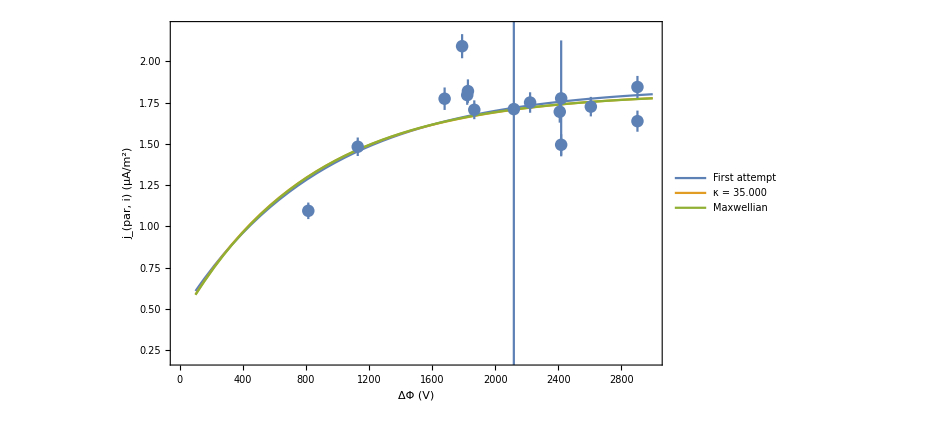

```mathematica
Show[Plot[{at1,kFit[pot],gFit[pot]},{pot,100,3000},PlotRange->{{0,3000},{0.2,2.2}},PlotLegends->((Style[#,20])&/@{"First attempt",StringForm["κ = `1`",NumberForm[kBestKappa,{3,3}]],"Maxwellian"}),Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

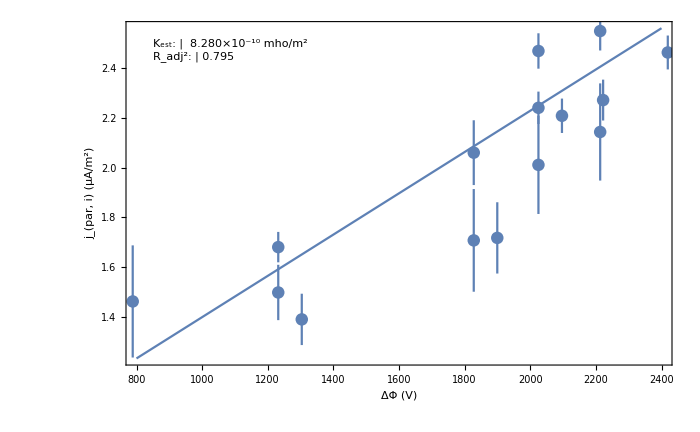

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

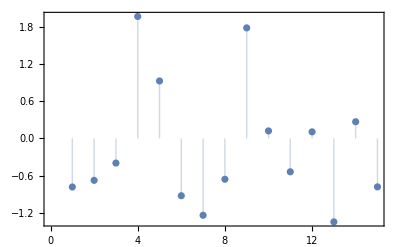

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

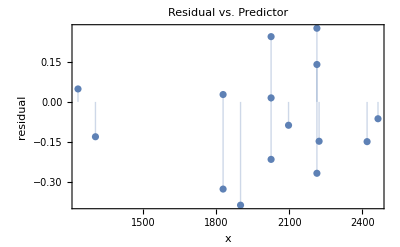

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Artificially combine parts of each

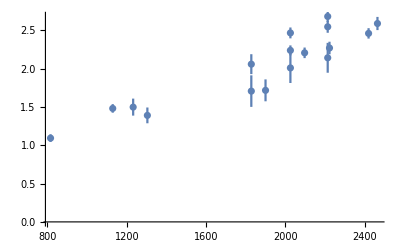

```mathematica
ErrorListPlot[errorData3]
```

## Simultaneously fit both sets of data, allowing RB to be different for each

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDat = Join[plotData1/.{x_,y_}->{1,x,y},plotData2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=plotDataWts1~Join~plotDataWts2;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gCombFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kCombConstraints={1<kFitRB1<300,1<kFitRB2<500,50<kFitT<500,0.1<kFitN<10,1.51<kFitKappa<35};
gCombConstraints={1<gFitRB1<300,1<gFitRB2<500,50<gFitT<500,0.1<gFitN<10};
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB1,3},{kFitRB2,10},{kFitT,300},{kFitN,1},{kFitKappa,5}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,(«1»)/(«1»),set==2,(0.0266987 0.834972 «19» «1» (1-(1-1/(«19»)) ((«1»«1»)^(«1»)) Gamma[1+35.])/((1-1/35.) («18»)^(3/2) Gamma[-1/2+35.])]]

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gCombConstraints},{{gFitRB1,3},{gFitRB2,10},{gFitT,300},{gFitN,1}},{set,pot},Weights->combWts]
```

FittedModel[Which[set==1,0.0266987 0.777027 («1») «18» √142.278,set==2,0.0266987 0.777027 (1-ⅇ^(-pot/((-1+«19») «19»)) (1-1/12.7063)) 12.7063 √142.278]]

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB1,kCombRB2,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF}
```

{6.17622,10.7058,187.539,0.834972,35.,6.12727}

```mathematica
{gCombRB1,gCombRB2,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF}
```

{7.52797,12.7063,142.278,0.777027,5.8886}

```mathematica
RBinit1=gCombRB1;RBinit2=gCombRB2;Tminit=gCombT;nminit=gCombN;
```

### Mess ‘round

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB1,Tm,nm],JVKappa[pot,RB1,Tm,nm,kappa1]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",kappa1]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData1]],{{RB1,RBinit1},1.01,300},{{kappa1,kappainit},1.501,35}],Manipulate[Show[Plot[{JVMaxwellian[pot,RB2,Tm,nm],JVKappa[pot,RB2,Tm,nm,kappa2]},{pot,100,3000},PlotRange->{Full,{0.5,4}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",kappa2]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[errorData2]],{{RB2,RBinit2},1.01,300},{{kappa2,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```